# Set - Up

## Trade - Offs

```mathematica
(* Baseline transformed traits (no care)*)
muStar[params_]:=(θ/. params);
rStar[params_]:=(s*Exp[-(1-θ)])/. params;
nuStar[params_]:=(1-(1-ν0)*Exp[-(1-θ)])/. params;
sigmaJStar[params_]:=(1-(1-σJ0)*Exp[-(1-θ)])/. params;

(* Exponential trade-off*)
tradeOff["Exp"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*Exp[-a*c],r0*Exp[-c],1-(1-nu0b)*Exp[-c],1-(1-sigmaJ0b)*Exp[-a*c]}/. params];

(* Saturating trade-off*)
tradeOff["Saturating"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,V=0.9,Khalf=0.3,sigmaJMax=0.9,costR=0.8,costNu=0.8},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
{mu0*(1-(V*c)/(Khalf+c)),r0*Exp[-costR*c],1-(1-nu0b)*Exp[-costNu*c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*(c/(Khalf+c))}/. params];

(* Sigmoid trade-off*)
tradeOff["Sigmoid"][params_,c_]:=Module[{mu0,r0,nu0b,sigmaJ0b,k=10.,c0=0.3,sigmaJMax=1,L,L0,Lnorm},mu0=muStar[params];
r0=rStar[params];
nu0b=nuStar[params];
sigmaJ0b=sigmaJStar[params];
L[x_]:=1/(1+Exp[-k*(x-c0)]);
L0=L[0];
Lnorm[x_]:=(L[x]-L0)/(1-L0);
{mu0*(1-L[c]),r0*Exp[-c],1-(1-nu0b)*Exp[-c],sigmaJ0b+(sigmaJMax-sigmaJ0b)*Lnorm[c]}/. params];
```

## Optimal Parameters

```mathematica
baseParamsFecundity={θ->0.8,ν0->0.1,σJ0->0.323823,mE->0.2,K->250,a->6};

careVals=Range[0,2,0.02];
```

## Distribution

```mathematica
meanR=6;

fecundityDist[mean_,kappa_]:=GammaDistribution[kappa,mean/kappa];
```

## Functions

```mathematica
getFitFixedC[params_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:fixed care c=0.5*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,0.5];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]

getFitAtC[params_,c_,shape_String:"Exp"]:=Module[{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
(*resident:no care*)
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
(*mutant:care=c*)
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
(*resident equilibrium*)
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
(*Jacobian*)
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
(*dominant eigenvalue*)
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//N//Re;
V]
```

## Big Function

```mathematica
runFecundityCase[kappa_,n_,seed_,shape_String:"Exp"]:=Module[
{rVals,(*sampled fecundity values*)
paramSets,(*parameter sets with different r values*)
fitnessFixedC,(*fitness values at fixed care c=0.5*)
resultsFixedC,(*paired (r x fitness) values*)
fitnessByCare,(*fitness values across all care levels*)
meanByCare,(*mean fitness across care*)
sdByCare         (*standard deviation of fitness across care*)},

(*fix seed*)
SeedRandom[seed];

(*draw random fecundity values*)
rVals=RandomVariate[fecundityDist[meanR,kappa],n];

(*show sampled fecundity values*)Print[Histogram[rVals,20,AxesLabel->{"Fecundity (r)","Frequency"},PlotLabel->"Fecundity distribution ("<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*build parameter sets by replacing r*)
paramSets=Table[Join[baseParamsFecundity,{r->rval}],{rval,rVals}];

(*invasion fitness at fixed care c=0.5*)
fitnessFixedC=Table[getFitFixedC[paramSets[[i]],shape],{i,Length[paramSets]}];

(*pair r with fitness*)
resultsFixedC=Transpose[{rVals,fitnessFixedC}];

(*fitness vs fecundity at c=0.5*)Print[ListPlot[resultsFixedC,AxesLabel->{"Fecundity (r)","Fitness (λ)"},PlotRange->All,PlotLabel->"Fitness vs fecundity ("<>shape<>", c = 0.5, κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*invasion fitness across full care range*)
fitnessByCare=Table[{c,Table[getFitAtC[paramSets[[i]],c,shape],{i,Length[paramSets]}]},{c,careVals}];

(*mean fitness across care*)
meanByCare={#[[1]],Mean[#[[2]]]}&/@fitnessByCare;

(*standard deviation of fitness across care*)
sdByCare={#[[1]],StandardDeviation[#[[2]]]}&/@fitnessByCare;

(*mean fitness vs care*)Print[ListPlot[meanByCare,Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotRange->All,PlotLabel->"Mean fitness vs care (fecundity r, "<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

(*SD of fitness vs care*)Print[ListPlot[sdByCare,Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotRange->All,PlotLabel->"SD of fitness vs care (fecundity r, "<>shape<>", κ = "<>ToString[kappa]<>", n = "<>ToString[n]<>")"]];

{meanByCare,sdByCare}];
```

# Exponential

## Bulk Code

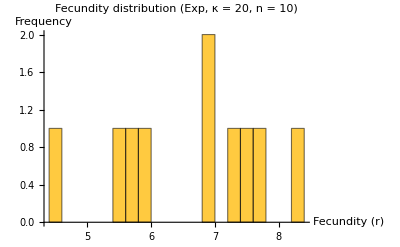

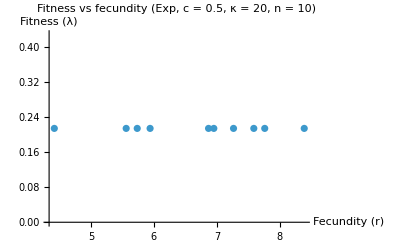

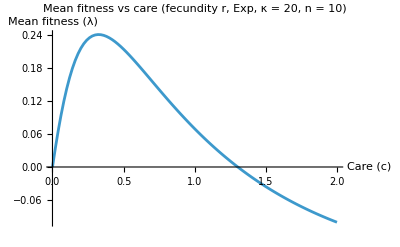

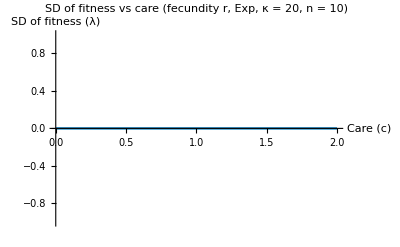

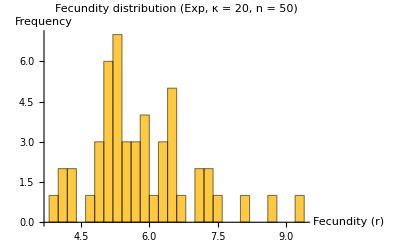

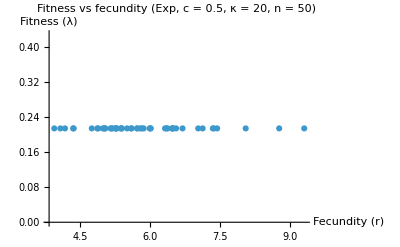

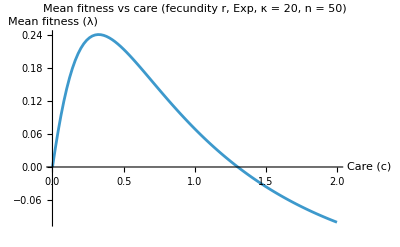

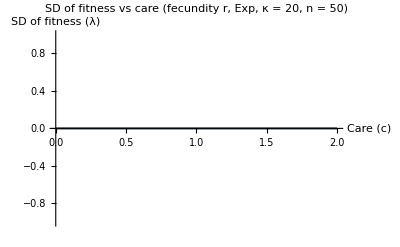

```mathematica
{meanFitnessByCareRA10Exp,sdFitnessByCareRA10Exp}=runFecundityCase[20,10,2010,"Exp"];

{meanFitnessByCareRA50Exp,sdFitnessByCareRA50Exp}=runFecundityCase[20,50,2050,"Exp"];

{meanFitnessByCareRA100Exp,sdFitnessByCareRA100Exp}=runFecundityCase[20,100,2100,"Exp"];



{meanFitnessByCareRB10Exp,sdFitnessByCareRB10Exp}=runFecundityCase[10,10,1010,"Exp"];

{meanFitnessByCareRB50Exp,sdFitnessByCareRB50Exp}=runFecundityCase[10,50,1050,"Exp"];

{meanFitnessByCareRB100Exp,sdFitnessByCareRB100Exp}=runFecundityCase[10,100,1100,"Exp"];


{meanFitnessByCareRC10Exp,sdFitnessByCareRC10Exp}=runFecundityCase[30,10,3010,"Exp"];

{meanFitnessByCareRC50Exp,sdFitnessByCareRC50Exp}=runFecundityCase[30,50,3050,"Exp"];

{meanFitnessByCareRC100Exp,sdFitnessByCareRC100Exp}=runFecundityCase[30,100,3100,"Exp"];
```

## Overlaid Plots

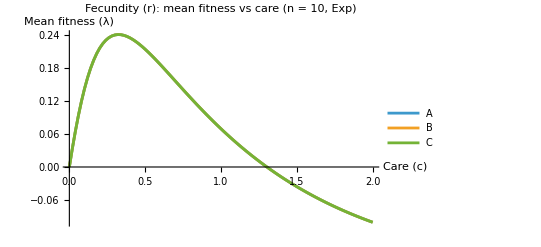

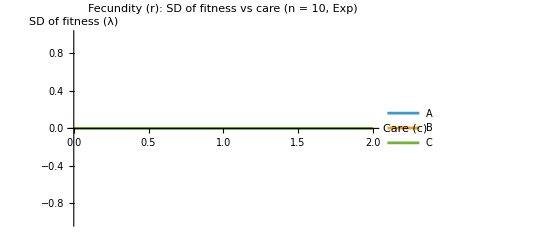

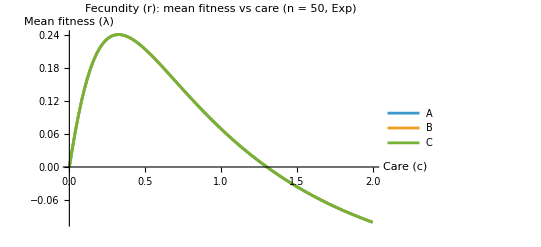

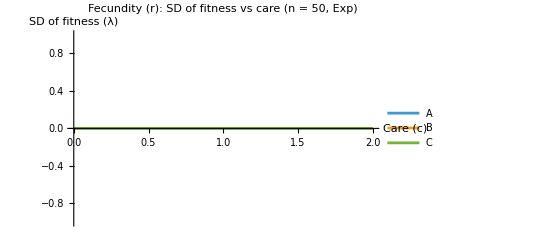

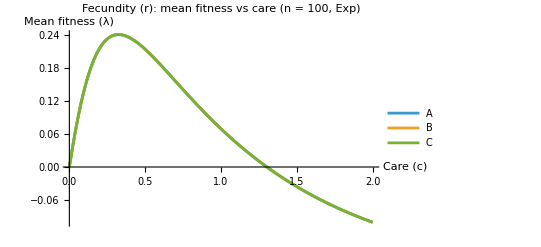

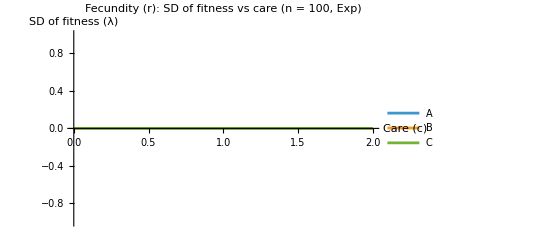

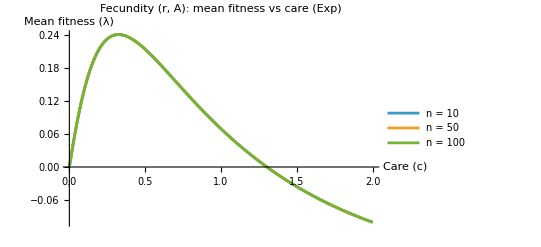

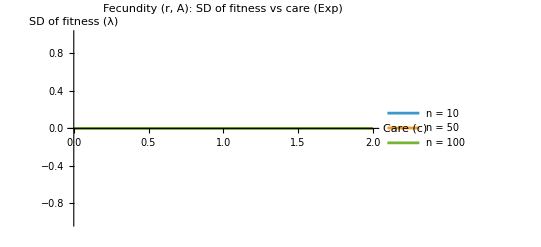

```mathematica
(*Grouped by sample size*)

ListPlot[{meanFitnessByCareRA10Exp,meanFitnessByCareRB10Exp,meanFitnessByCareRC10Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): mean fitness vs care (n = 10, Exp)"]

ListPlot[{sdFitnessByCareRA10Exp,sdFitnessByCareRB10Exp,sdFitnessByCareRC10Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): SD of fitness vs care (n = 10, Exp)"]


ListPlot[{meanFitnessByCareRA50Exp,meanFitnessByCareRB50Exp,meanFitnessByCareRC50Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): mean fitness vs care (n = 50, Exp)"]

ListPlot[{sdFitnessByCareRA50Exp,sdFitnessByCareRB50Exp,sdFitnessByCareRC50Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): SD of fitness vs care (n = 50, Exp)"]


ListPlot[{meanFitnessByCareRA100Exp,meanFitnessByCareRB100Exp,meanFitnessByCareRC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): mean fitness vs care (n = 100, Exp)"]

ListPlot[{sdFitnessByCareRA100Exp,sdFitnessByCareRB100Exp,sdFitnessByCareRC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotRange->All,PlotLabel->"Fecundity (r): SD of fitness vs care (n = 100, Exp)"]



(*Grouped by distribution*)

ListPlot[{meanFitnessByCareRA10Exp,meanFitnessByCareRA50Exp,meanFitnessByCareRA100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, A): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareRA10Exp,sdFitnessByCareRA50Exp,sdFitnessByCareRA100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, A): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareRB10Exp,meanFitnessByCareRB50Exp,meanFitnessByCareRB100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, B): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareRB10Exp,sdFitnessByCareRB50Exp,sdFitnessByCareRB100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, B): SD of fitness vs care (Exp)"]


ListPlot[{meanFitnessByCareRC10Exp,meanFitnessByCareRC50Exp,meanFitnessByCareRC100Exp},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, C): mean fitness vs care (Exp)"]

ListPlot[{sdFitnessByCareRC10Exp,sdFitnessByCareRC50Exp,sdFitnessByCareRC100Exp},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotRange->All,PlotLabel->"Fecundity (r, C): SD of fitness vs care (Exp)"]
```

## Tables

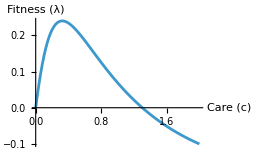
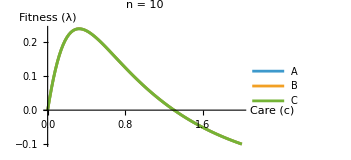
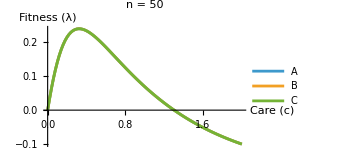
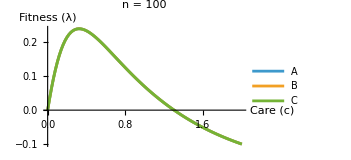
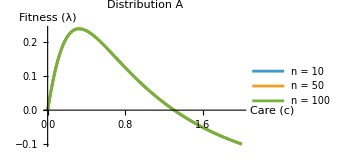
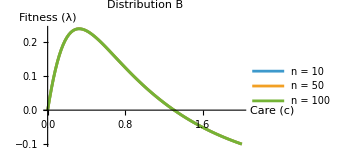
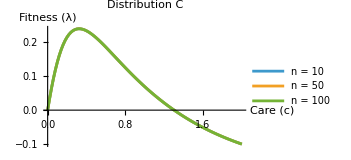
Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

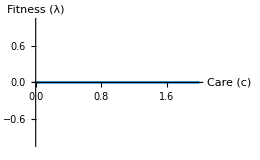
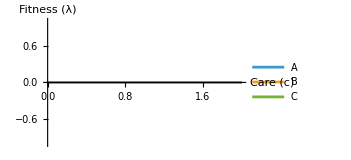
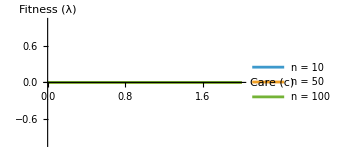
SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
plotOpts={Joined->True,PlotRange->All,AxesLabel->{"Care (c)","Fitness (λ)"},ImageSize->260};
meanRA10Exp=ListPlot[{meanFitnessByCareRA10Exp,meanFitnessByCareRB10Exp,meanFitnessByCareRC10Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanRA50Exp=ListPlot[{meanFitnessByCareRA50Exp,meanFitnessByCareRB50Exp,meanFitnessByCareRC50Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanRA100Exp=ListPlot[{meanFitnessByCareRA100Exp,meanFitnessByCareRB100Exp,meanFitnessByCareRC100Exp},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanRCompAExp=ListPlot[{meanFitnessByCareRA10Exp,meanFitnessByCareRA50Exp,meanFitnessByCareRA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanRCompBExp=ListPlot[{meanFitnessByCareRB10Exp,meanFitnessByCareRB50Exp,meanFitnessByCareRB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanRCompCExp=ListPlot[{meanFitnessByCareRC10Exp,meanFitnessByCareRC50Exp,meanFitnessByCareRC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableRExp=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareRA10Exp},plotOpts],ListPlot[{meanFitnessByCareRB10Exp},plotOpts],ListPlot[{meanFitnessByCareRC10Exp},plotOpts],meanRA10Exp},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareRA50Exp},plotOpts],ListPlot[{meanFitnessByCareRB50Exp},plotOpts],ListPlot[{meanFitnessByCareRC50Exp},plotOpts],meanRA50Exp},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareRA100Exp},plotOpts],ListPlot[{meanFitnessByCareRB100Exp},plotOpts],ListPlot[{meanFitnessByCareRC100Exp},plotOpts],meanRA100Exp},{Style["Compiled",Bold],meanRCompAExp,meanRCompBExp,meanRCompCExp,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableRExp=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareRA10Exp},plotOpts],ListPlot[{sdFitnessByCareRB10Exp},plotOpts],ListPlot[{sdFitnessByCareRC10Exp},plotOpts],ListPlot[{sdFitnessByCareRA10Exp,sdFitnessByCareRB10Exp,sdFitnessByCareRC10Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareRA50Exp},plotOpts],ListPlot[{sdFitnessByCareRB50Exp},plotOpts],ListPlot[{sdFitnessByCareRC50Exp},plotOpts],ListPlot[{sdFitnessByCareRA50Exp,sdFitnessByCareRB50Exp,sdFitnessByCareRC50Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareRA100Exp},plotOpts],ListPlot[{sdFitnessByCareRB100Exp},plotOpts],ListPlot[{sdFitnessByCareRC100Exp},plotOpts],ListPlot[{sdFitnessByCareRA100Exp,sdFitnessByCareRB100Exp,sdFitnessByCareRC100Exp},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareRA10Exp,sdFitnessByCareRA50Exp,sdFitnessByCareRA100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRB10Exp,sdFitnessByCareRB50Exp,sdFitnessByCareRB100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRC10Exp,sdFitnessByCareRC50Exp,sdFitnessByCareRC100Exp},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableRExp
sdTableRExp
```

## Big Plots

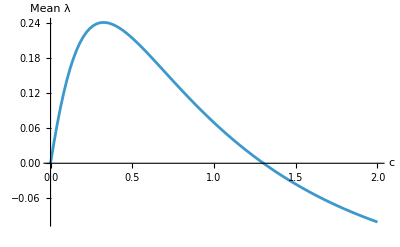

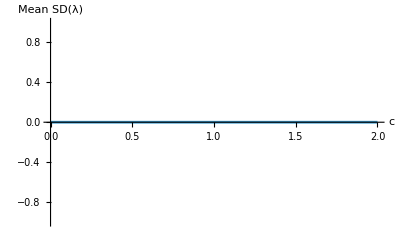

```mathematica
allMeanCurvesRExp={meanFitnessByCareRA10Exp,meanFitnessByCareRA50Exp,meanFitnessByCareRA100Exp,meanFitnessByCareRB10Exp,meanFitnessByCareRB50Exp,meanFitnessByCareRB100Exp,meanFitnessByCareRC10Exp,meanFitnessByCareRC50Exp,meanFitnessByCareRC100Exp};

allSDCurvesRExp={sdFitnessByCareRA10Exp,sdFitnessByCareRA50Exp,sdFitnessByCareRA100Exp,sdFitnessByCareRB10Exp,sdFitnessByCareRB50Exp,sdFitnessByCareRB100Exp,sdFitnessByCareRC10Exp,sdFitnessByCareRC50Exp,sdFitnessByCareRC100Exp};

careValuesRExp=allMeanCurvesRExp[[1]][[All,1]];

overallMeanRExp=Transpose[{careValuesRExp,Mean/@Transpose[allMeanCurvesRExp[[All,All,2]]]}];

overallSDRExp=Transpose[{careValuesRExp,Mean/@Transpose[allSDCurvesRExp[[All,All,2]]]}];

plotOverallMeanRExp=ListPlot[overallMeanRExp,Joined->True,PlotRange->All,AxesLabel->{"c","Mean λ"}];

plotOverallSDRExp=ListPlot[overallSDRExp,Joined->True,PlotRange->All,AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanRExp
plotOverallSDRExp
```

# Saturating

## Bulk Code

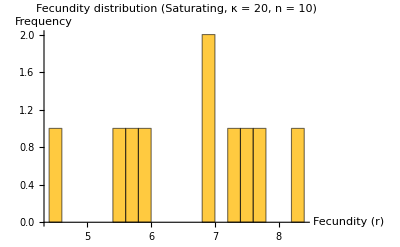

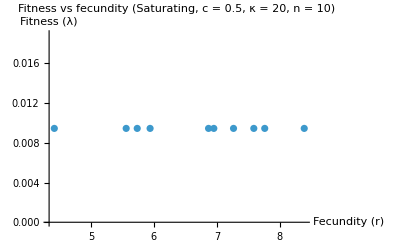

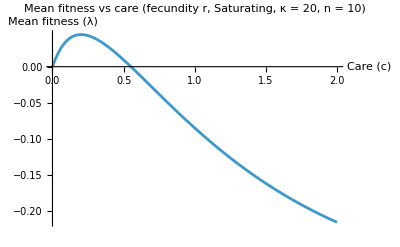

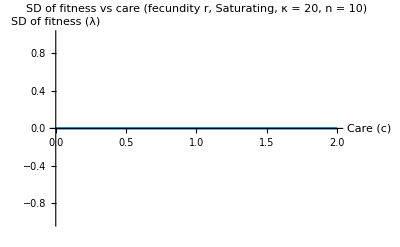

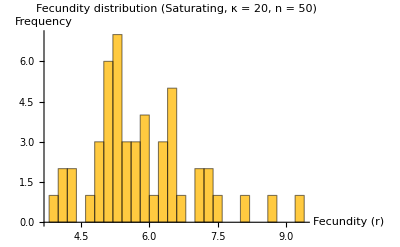

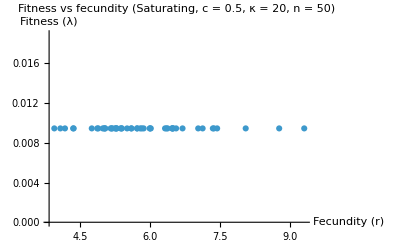

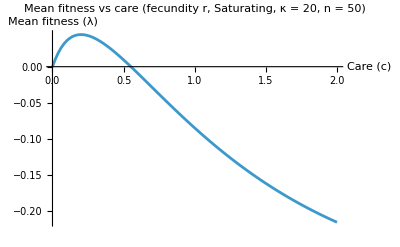

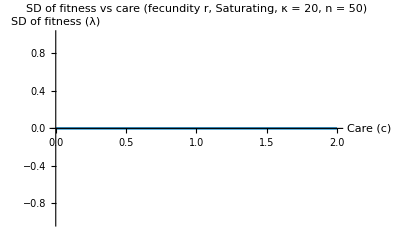

```mathematica
{meanFitnessByCareRA10Sat,sdFitnessByCareRA10Sat}=runFecundityCase[20,10,2010,"Saturating"];

{meanFitnessByCareRA50Sat,sdFitnessByCareRA50Sat}=runFecundityCase[20,50,2050,"Saturating"];

{meanFitnessByCareRA100Sat,sdFitnessByCareRA100Sat}=runFecundityCase[20,100,2100,"Saturating"];


{meanFitnessByCareRB10Sat,sdFitnessByCareRB10Sat}=runFecundityCase[10,10,1010,"Saturating"];

{meanFitnessByCareRB50Sat,sdFitnessByCareRB50Sat}=runFecundityCase[10,50,1050,"Saturating"];

{meanFitnessByCareRB100Sat,sdFitnessByCareRB100Sat}=runFecundityCase[10,100,1100,"Saturating"];


{meanFitnessByCareRC10Sat,sdFitnessByCareRC10Sat}=runFecundityCase[30,10,3010,"Saturating"];

{meanFitnessByCareRC50Sat,sdFitnessByCareRC50Sat}=runFecundityCase[30,50,3050,"Saturating"];

{meanFitnessByCareRC100Sat,sdFitnessByCareRC100Sat}=runFecundityCase[30,100,3100,"Saturating"];
```

## Diagnostic Plots

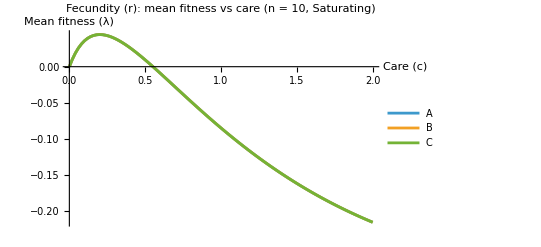

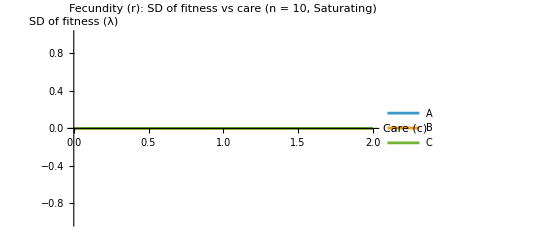

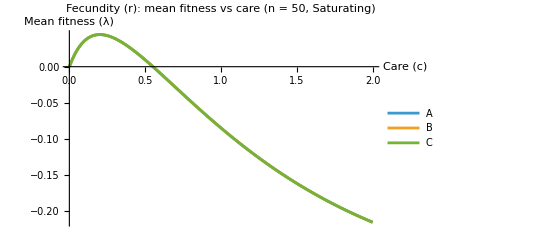

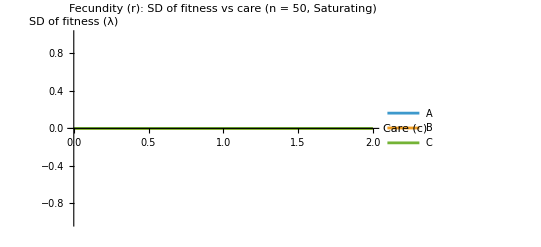

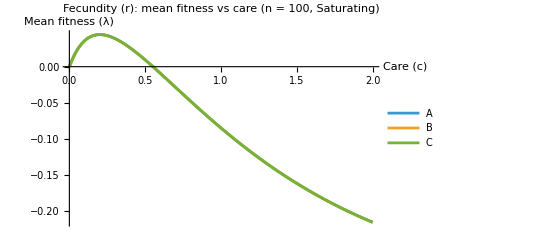

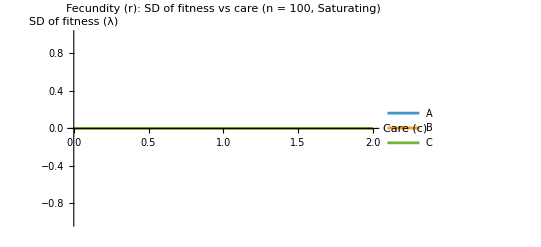

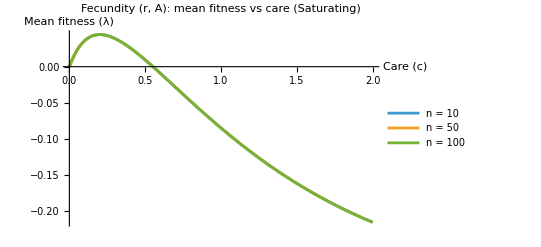

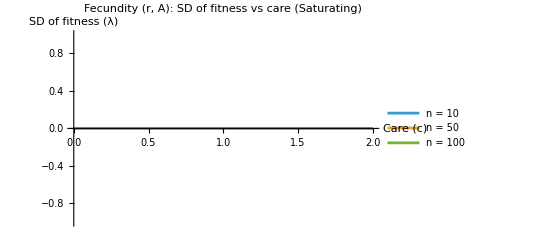

```mathematica
(*grouped by sample size*)

ListPlot[{meanFitnessByCareRA10Sat,meanFitnessByCareRB10Sat,meanFitnessByCareRC10Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 10, Saturating)"]

ListPlot[{sdFitnessByCareRA10Sat,sdFitnessByCareRB10Sat,sdFitnessByCareRC10Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 10, Saturating)"]


ListPlot[{meanFitnessByCareRA50Sat,meanFitnessByCareRB50Sat,meanFitnessByCareRC50Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 50, Saturating)"]

ListPlot[{sdFitnessByCareRA50Sat,sdFitnessByCareRB50Sat,sdFitnessByCareRC50Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 50, Saturating)"]


ListPlot[{meanFitnessByCareRA100Sat,meanFitnessByCareRB100Sat,meanFitnessByCareRC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 100, Saturating)"]

ListPlot[{sdFitnessByCareRA100Sat,sdFitnessByCareRB100Sat,sdFitnessByCareRC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 100, Saturating)"]


(*grouped by distribution*)

ListPlot[{meanFitnessByCareRA10Sat,meanFitnessByCareRA50Sat,meanFitnessByCareRA100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, A): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareRA10Sat,sdFitnessByCareRA50Sat,sdFitnessByCareRA100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, A): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareRB10Sat,meanFitnessByCareRB50Sat,meanFitnessByCareRB100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, B): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareRB10Sat,sdFitnessByCareRB50Sat,sdFitnessByCareRB100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, B): SD of fitness vs care (Saturating)"]


ListPlot[{meanFitnessByCareRC10Sat,meanFitnessByCareRC50Sat,meanFitnessByCareRC100Sat},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, C): mean fitness vs care (Saturating)"]

ListPlot[{sdFitnessByCareRC10Sat,sdFitnessByCareRC50Sat,sdFitnessByCareRC100Sat},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, C): SD of fitness vs care (Saturating)"]
```

## Tables

```mathematica
meanRA10Sat=ListPlot[{meanFitnessByCareRA10Sat,meanFitnessByCareRB10Sat,meanFitnessByCareRC10Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanRA50Sat=ListPlot[{meanFitnessByCareRA50Sat,meanFitnessByCareRB50Sat,meanFitnessByCareRC50Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanRA100Sat=ListPlot[{meanFitnessByCareRA100Sat,meanFitnessByCareRB100Sat,meanFitnessByCareRC100Sat},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanRCompASat=ListPlot[{meanFitnessByCareRA10Sat,meanFitnessByCareRA50Sat,meanFitnessByCareRA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanRCompBSat=ListPlot[{meanFitnessByCareRB10Sat,meanFitnessByCareRB50Sat,meanFitnessByCareRB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanRCompCSat=ListPlot[{meanFitnessByCareRC10Sat,meanFitnessByCareRC50Sat,meanFitnessByCareRC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableRSat=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareRA10Sat},plotOpts],ListPlot[{meanFitnessByCareRB10Sat},plotOpts],ListPlot[{meanFitnessByCareRC10Sat},plotOpts],meanRA10Sat},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareRA50Sat},plotOpts],ListPlot[{meanFitnessByCareRB50Sat},plotOpts],ListPlot[{meanFitnessByCareRC50Sat},plotOpts],meanRA50Sat},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareRA100Sat},plotOpts],ListPlot[{meanFitnessByCareRB100Sat},plotOpts],ListPlot[{meanFitnessByCareRC100Sat},plotOpts],meanRA100Sat},{Style["Compiled",Bold],meanRCompASat,meanRCompBSat,meanRCompCSat,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableRSat=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareRA10Sat},plotOpts],ListPlot[{sdFitnessByCareRB10Sat},plotOpts],ListPlot[{sdFitnessByCareRC10Sat},plotOpts],ListPlot[{sdFitnessByCareRA10Sat,sdFitnessByCareRB10Sat,sdFitnessByCareRC10Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareRA50Sat},plotOpts],ListPlot[{sdFitnessByCareRB50Sat},plotOpts],ListPlot[{sdFitnessByCareRC50Sat},plotOpts],ListPlot[{sdFitnessByCareRA50Sat,sdFitnessByCareRB50Sat,sdFitnessByCareRC50Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareRA100Sat},plotOpts],ListPlot[{sdFitnessByCareRB100Sat},plotOpts],ListPlot[{sdFitnessByCareRC100Sat},plotOpts],ListPlot[{sdFitnessByCareRA100Sat,sdFitnessByCareRB100Sat,sdFitnessByCareRC100Sat},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareRA10Sat,sdFitnessByCareRA50Sat,sdFitnessByCareRA100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRB10Sat,sdFitnessByCareRB50Sat,sdFitnessByCareRB100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRC10Sat,sdFitnessByCareRC50Sat,sdFitnessByCareRC100Sat},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableRSat
sdTableRSat
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesRSat={meanFitnessByCareRA10Sat,meanFitnessByCareRA50Sat,meanFitnessByCareRA100Sat,meanFitnessByCareRB10Sat,meanFitnessByCareRB50Sat,meanFitnessByCareRB100Sat,meanFitnessByCareRC10Sat,meanFitnessByCareRC50Sat,meanFitnessByCareRC100Sat};

allSDCurvesRSat={sdFitnessByCareRA10Sat,sdFitnessByCareRA50Sat,sdFitnessByCareRA100Sat,sdFitnessByCareRB10Sat,sdFitnessByCareRB50Sat,sdFitnessByCareRB100Sat,sdFitnessByCareRC10Sat,sdFitnessByCareRC50Sat,sdFitnessByCareRC100Sat};

careValuesRSat=allMeanCurvesRSat[[1]][[All,1]];

overallMeanRSat=Transpose[{careValuesRSat,Mean/@Transpose[allMeanCurvesRSat[[All,All,2]]]}];

overallSDRSat=Transpose[{careValuesRSat,Mean/@Transpose[allSDCurvesRSat[[All,All,2]]]}];

plotOverallMeanRSat=ListPlot[overallMeanRSat,Joined->True,PlotRange->All,AxesLabel->{"c","Mean λ"}];

plotOverallSDRSat=ListPlot[overallSDRSat,Joined->True,PlotRange->All,AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanRSat
plotOverallSDRSat
```

-Graphics-

-Graphics-

# Sigmoid

## Bulk Code

```mathematica
{meanFitnessByCareRA10Sig,sdFitnessByCareRA10Sig}=runFecundityCase[20,10,2010,"Sigmoid"];

{meanFitnessByCareRA50Sig,sdFitnessByCareRA50Sig}=runFecundityCase[20,50,2050,"Sigmoid"];

{meanFitnessByCareRA100Sig,sdFitnessByCareRA100Sig}=runFecundityCase[20,100,2100,"Sigmoid"];



{meanFitnessByCareRB10Sig,sdFitnessByCareRB10Sig}=runFecundityCase[10,10,1010,"Sigmoid"];

{meanFitnessByCareRB50Sig,sdFitnessByCareRB50Sig}=runFecundityCase[10,50,1050,"Sigmoid"];

{meanFitnessByCareRB100Sig,sdFitnessByCareRB100Sig}=runFecundityCase[10,100,1100,"Sigmoid"];



{meanFitnessByCareRC10Sig,sdFitnessByCareRC10Sig}=runFecundityCase[30,10,3010,"Sigmoid"];

{meanFitnessByCareRC50Sig,sdFitnessByCareRC50Sig}=runFecundityCase[30,50,3050,"Sigmoid"];

{meanFitnessByCareRC100Sig,sdFitnessByCareRC100Sig}=runFecundityCase[30,100,3100,"Sigmoid"];
```

-Graphics-

-Graphics-

-Graphics-

«33 more identical outputs»

## Diagnostic Plots

```mathematica
(*grouped by sample size*)
ListPlot[{meanFitnessByCareRA10Sig,meanFitnessByCareRB10Sig,meanFitnessByCareRC10Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 10, Sigmoid)"]

ListPlot[{sdFitnessByCareRA10Sig,sdFitnessByCareRB10Sig,sdFitnessByCareRC10Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 10, Sigmoid)"]


ListPlot[{meanFitnessByCareRA50Sig,meanFitnessByCareRB50Sig,meanFitnessByCareRC50Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 50, Sigmoid)"]

ListPlot[{sdFitnessByCareRA50Sig,sdFitnessByCareRB50Sig,sdFitnessByCareRC50Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 50, Sigmoid)"]


ListPlot[{meanFitnessByCareRA100Sig,meanFitnessByCareRB100Sig,meanFitnessByCareRC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): mean fitness vs care (n = 100, Sigmoid)"]

ListPlot[{sdFitnessByCareRA100Sig,sdFitnessByCareRB100Sig,sdFitnessByCareRC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"A","B","C"},PlotLabel->"Fecundity (r): SD of fitness vs care (n = 100, Sigmoid)"]


(*grouped by distribution*)

ListPlot[{meanFitnessByCareRA10Sig,meanFitnessByCareRA50Sig,meanFitnessByCareRA100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, A): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareRA10Sig,sdFitnessByCareRA50Sig,sdFitnessByCareRA100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, A): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareRB10Sig,meanFitnessByCareRB50Sig,meanFitnessByCareRB100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, B): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareRB10Sig,sdFitnessByCareRB50Sig,sdFitnessByCareRB100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, B): SD of fitness vs care (Sigmoid)"]


ListPlot[{meanFitnessByCareRC10Sig,meanFitnessByCareRC50Sig,meanFitnessByCareRC100Sig},Joined->True,AxesLabel->{"Care (c)","Mean fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, C): mean fitness vs care (Sigmoid)"]

ListPlot[{sdFitnessByCareRC10Sig,sdFitnessByCareRC50Sig,sdFitnessByCareRC100Sig},Joined->True,AxesLabel->{"Care (c)","SD of fitness (λ)"},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Fecundity (r, C): SD of fitness vs care (Sigmoid)"]
```

-Graphics-

-Graphics-

-Graphics-

«9 more identical outputs»

## Tables

```mathematica
meanRA10Sig=ListPlot[{meanFitnessByCareRA10Sig,meanFitnessByCareRB10Sig,meanFitnessByCareRC10Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 10",plotOpts];

meanRA50Sig=ListPlot[{meanFitnessByCareRA50Sig,meanFitnessByCareRB50Sig,meanFitnessByCareRC50Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 50",plotOpts];

meanRA100Sig=ListPlot[{meanFitnessByCareRA100Sig,meanFitnessByCareRB100Sig,meanFitnessByCareRC100Sig},PlotLegends->{"A","B","C"},PlotLabel->"n = 100",plotOpts];

meanRCompASig=ListPlot[{meanFitnessByCareRA10Sig,meanFitnessByCareRA50Sig,meanFitnessByCareRA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution A",plotOpts];

meanRCompBSig=ListPlot[{meanFitnessByCareRB10Sig,meanFitnessByCareRB50Sig,meanFitnessByCareRB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution B",plotOpts];

meanRCompCSig=ListPlot[{meanFitnessByCareRC10Sig,meanFitnessByCareRC50Sig,meanFitnessByCareRC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},PlotLabel->"Distribution C",plotOpts];

meanTableRSig=Grid[{{Style["Mean",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{meanFitnessByCareRA10Sig},plotOpts],ListPlot[{meanFitnessByCareRB10Sig},plotOpts],ListPlot[{meanFitnessByCareRC10Sig},plotOpts],meanRA10Sig},{Style["N = 50",Bold],ListPlot[{meanFitnessByCareRA50Sig},plotOpts],ListPlot[{meanFitnessByCareRB50Sig},plotOpts],ListPlot[{meanFitnessByCareRC50Sig},plotOpts],meanRA50Sig},{Style["N = 100",Bold],ListPlot[{meanFitnessByCareRA100Sig},plotOpts],ListPlot[{meanFitnessByCareRB100Sig},plotOpts],ListPlot[{meanFitnessByCareRC100Sig},plotOpts],meanRA100Sig},{Style["Compiled",Bold],meanRCompASig,meanRCompBSig,meanRCompCSig,Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

sdTableRSig=Grid[{{Style["SD",16,Bold,Background->LightPink],Style["Distribution A",Bold],Style["Distribution B",Bold],Style["Distribution C",Bold],Style["Compiled",Bold]},{Style["N = 10",Bold],ListPlot[{sdFitnessByCareRA10Sig},plotOpts],ListPlot[{sdFitnessByCareRB10Sig},plotOpts],ListPlot[{sdFitnessByCareRC10Sig},plotOpts],ListPlot[{sdFitnessByCareRA10Sig,sdFitnessByCareRB10Sig,sdFitnessByCareRC10Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 50",Bold],ListPlot[{sdFitnessByCareRA50Sig},plotOpts],ListPlot[{sdFitnessByCareRB50Sig},plotOpts],ListPlot[{sdFitnessByCareRC50Sig},plotOpts],ListPlot[{sdFitnessByCareRA50Sig,sdFitnessByCareRB50Sig,sdFitnessByCareRC50Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["N = 100",Bold],ListPlot[{sdFitnessByCareRA100Sig},plotOpts],ListPlot[{sdFitnessByCareRB100Sig},plotOpts],ListPlot[{sdFitnessByCareRC100Sig},plotOpts],ListPlot[{sdFitnessByCareRA100Sig,sdFitnessByCareRB100Sig,sdFitnessByCareRC100Sig},PlotLegends->{"A","B","C"},plotOpts]},{Style["Compiled",Bold],ListPlot[{sdFitnessByCareRA10Sig,sdFitnessByCareRA50Sig,sdFitnessByCareRA100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRB10Sig,sdFitnessByCareRB50Sig,sdFitnessByCareRB100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],ListPlot[{sdFitnessByCareRC10Sig,sdFitnessByCareRC50Sig,sdFitnessByCareRC100Sig},PlotLegends->{"n = 10","n = 50","n = 100"},plotOpts],Graphics[{}]}},Frame->All,Spacings->{2,2},Alignment->Center];

meanTableRSig
sdTableRSig
```

Mean | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

SD | Distribution A | Distribution B | Distribution C | Compiled
N = 10 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 50 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
N = 100 | -Graphics- | -Graphics- | -Graphics- | -Graphics-
Compiled | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Big Plots

```mathematica
allMeanCurvesRSig={meanFitnessByCareRA10Sig,meanFitnessByCareRA50Sig,meanFitnessByCareRA100Sig,meanFitnessByCareRB10Sig,meanFitnessByCareRB50Sig,meanFitnessByCareRB100Sig,meanFitnessByCareRC10Sig,meanFitnessByCareRC50Sig,meanFitnessByCareRC100Sig};

allSDCurvesRSig={sdFitnessByCareRA10Sig,sdFitnessByCareRA50Sig,sdFitnessByCareRA100Sig,sdFitnessByCareRB10Sig,sdFitnessByCareRB50Sig,sdFitnessByCareRB100Sig,sdFitnessByCareRC10Sig,sdFitnessByCareRC50Sig,sdFitnessByCareRC100Sig};

careValuesRSig=allMeanCurvesRSig[[1]][[All,1]];

overallMeanRSig=Transpose[{careValuesRSig,Mean/@Transpose[allMeanCurvesRSig[[All,All,2]]]}];

overallSDRSig=Transpose[{careValuesRSig,Mean/@Transpose[allSDCurvesRSig[[All,All,2]]]}];

plotOverallMeanRSig=ListPlot[overallMeanRSig,Joined->True,PlotRange->All,AxesLabel->{"c","Mean λ"}];

plotOverallSDRSig=ListPlot[overallSDRSig,Joined->True,PlotRange->All,AxesLabel->{"c","Mean SD(λ)"}];

plotOverallMeanRSig
plotOverallSDRSig
```

-Graphics-

-Graphics-

# Deterministic Shape

```mathematica
Aexpr[th_,v0_,sj_,ss_,me_,Kval_:250]:=Kval*(1-(((v0/sj)*(1+(th/me)))/ss));


(*Care mutant invading no-care resident*)
getFit[params_,shape_String:"Exp"]:=Module[
{μres,rres,νres,σJres,μmut,rmut,νmut,σJmut,A,mat,res,V},
{μres,rres,νres,σJres}=tradeOff[shape][params,0];
{μmut,rmut,νmut,σJmut}=tradeOff[shape][params,c];
A=(K*(1-(((νres/σJres)*(1+(μres/mE)))/rres)))/. params//N;
mat={{-λ-mE-μmut,rmut*(1-A/K)},{mE*σJmut,-λ-νmut}}/. params;
res=NSolve[Det[mat]==0,λ];
V=(λ/. res[[2]])/. params//Simplify;
Table[{val,Re[N[V/. c->val]]},{val,0,2,0.01}]];

params1={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};
params2={θ->0.7999967491603689,ν0->0.10000440803427434,σJ0->0.32383733876731385,s->5.999984154933559,mE->0.19999923208705223,K->250,a->6};
params3={θ->0.8,ν0->0.1,σJ0->0.32383733876731385,s->6,mE->0.2,K->250,a->6};

fit1=getFit[params1,"Exp"];
fit2=getFit[params2,"Saturating"];
fit3=getFit[params3,"Sigmoid"];

plotExp=ListPlot[fit1,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSaturating=ListPlot[fit2,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];
plotSigmoid=ListPlot[fit3,Joined->True,PlotRange->All,AxesLabel->{"c","λ"}];

plotExp
plotSaturating
plotSigmoid
```

-Graphics-

-Graphics-

-Graphics-

# Overall Figure

```mathematica
allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],overallMeanRSat[[All,2]],overallMeanRSig[[All,2]],fit1[[All,2]],fit2[[All,2]],fit3[[All,2]]}];

minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};

allSDValues=Flatten[{overallSDRExp[[All,2]],overallSDRSat[[All,2]],overallSDRSig[[All,2]]}];

minSDY=Min[allSDValues];
maxSDY=Max[allSDValues];
rangeSD=maxSDY-minSDY;
paddingSD=If[rangeSD==0,0.1,0.05*rangeSD];
sdYRange={minSDY-paddingSD,maxSDY+paddingSD};

addPanelLabel[plt_,lab_]:=Show[plt,Epilog->Inset[Style["("<>lab<>")",14,Bold],Scaled[{0.5,1}],{Left,Top}]];

makeOverlay[fit_,mean_,lab_]:=addPanelLabel[ListPlot[{fit,mean},Joined->True,PlotRange->{{0,2},meanYRange},AxesLabel->{"c","λ"},PlotLegends->Placed[{"Deterministic","Stochastic"},Above]],lab];

makeSD[sd_,lab_]:=addPanelLabel[ListPlot[sd,Joined->True,PlotRange->{{0,2},sdYRange},AxesLabel->{"c","Mean SD(λ)"},PlotStyle->Directive[Darker[Green],Thick]],lab];


overlayExp=makeOverlay[fit1,overallMeanRExp,"a"];
overlaySat=makeOverlay[fit2,overallMeanRSat,"b"];
overlaySig=makeOverlay[fit3,overallMeanRSig,"c"];

sdExp=makeSD[overallSDRExp,"b"];
sdSat=makeSD[overallSDRSat,"e"];
sdSig=makeSD[overallSDRSig,"f"];

overlayExp
overlaySat
overlaySig
sdExp
sdSat
sdSig
```

-Graphics-

-Graphics-

-Graphics-

«3 more identical outputs»

```mathematica
imgW=520;
imgH=260;

overlayExpSized=Show[overlayExp,ImageSize->{imgW,imgH}];
overlaySatSized=Show[overlaySat,ImageSize->{imgW,imgH}];
overlaySigSized=Show[overlaySig,ImageSize->{imgW,imgH}];

sdExpSized=Show[sdExp,ImageSize->{imgW,imgH}];
sdSatSized=Show[sdSat,ImageSize->{imgW,imgH}];
sdSigSized=Show[sdSig,ImageSize->{imgW,imgH}];

finalFigure=GraphicsGrid[{{Style["Exponential",18, Bold],Style["Saturating",18, Bold],Style["Sigmoid",18, Bold]},{overlayExpSized,overlaySatSized,overlaySigSized},{sdExpSized,sdSatSized,sdSigSized}},Spacings->{2,2},Alignment->{Center,Center}];

finalFigure
```

-Graphics-

## Exponential Only

```mathematica
allMeanDetValues=Flatten[{overallMeanRExp[[All,2]],fit1[[All,2]]}];

minMeanY=Min[allMeanDetValues];
maxMeanY=Max[allMeanDetValues];
rangeMean=maxMeanY-minMeanY;
paddingMean=If[rangeMean==0,0.1,0.05*rangeMean];
meanYRange={minMeanY-paddingMean,maxMeanY+paddingMean};

allSDValues=overallSDRExp[[All,2]];

minSDY=Min[allSDValues];
maxSDY=Max[allSDValues];
rangeSD=maxSDY-minSDY;
paddingSD=If[rangeSD==0,0.1,0.05*rangeSD];
sdYRange={minSDY-paddingSD,maxSDY+paddingSD};


colDet=RGBColor[0.368,0.507,0.710];
colSto=RGBColor[0.881,0.611,0.142];
colSD=RGBColor[0,0.35,0];


addPanelLabel[plt_,lab_]:=Show[plt,Epilog->{Inset[Style["("<>lab<>")",14,Bold],Scaled[{0.5,0.95}]]}];


makeOverlay[fit_,mean_,lab_]:=Legended[addPanelLabel[ListPlot[{fit,mean},Joined->True,PlotStyle->{Directive[colDet,Thick],Directive[colSto,Thick]},PlotRange->{{0,2},meanYRange},AxesLabel->{Style["c",15],Style["λ",15]},LabelStyle->Directive[Black,14],ImageSize->500,ImagePadding->{{60,20},{40,40}}],lab],Placed[LineLegend[{Directive[colDet,Thick],Directive[colSto,Thick]},{"Deterministic","Stochastic"},LabelStyle->Directive[14],LegendMarkerSize->30,LegendLayout->"Row"],Above]];


makeSD[sd_,lab_]:=Legended[addPanelLabel[ListPlot[sd,Joined->True,PlotRange->{{0,2},sdYRange},AxesLabel->{Style["c",15],Style["Mean SD(λ)",15]},LabelStyle->Directive[Black,14],PlotStyle->Directive[colSD,Thick],ImageSize->500,ImagePadding->{{60,20},{40,40}}],lab],Placed[LineLegend[{Directive[colSD,Thick]},{"SD(λ)"},LabelStyle->Directive[14],LegendMarkerSize->30,LegendLayout->"Row"],Above]];


overlayExp=makeOverlay[fit1,overallMeanRExp,"a"];
sdExp=makeSD[overallSDRExp,"b"];

combinedExpFigure=GraphicsColumn[{overlayExp,sdExp},Spacings->1.5,Alignment->Center];

combinedExpFigure
```

-Graphics-